# Non classical light and quadratures

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[Table[If[i==j+1,Sqrt[i-1],0],{i,1,n},{j,1,n}],n];
ca=aa["Dagger"];
{ca,aa}]
fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
commutator[a_QuantumOperator,b_QuantumOperator]:=a@b - b@a 
operatorVariance[state_QuantumState, op_QuantumOperator]:= (state["Dagger"]@ (op @ op)@ state)["Scalar"] - (state["Dagger"]@ op @ state)["Scalar"]^2
```

```mathematica
X1 := 1/2(a+a["Dagger"]);
X2 := 1/(2I)(a-a["Dagger"]);
coherentTrunc[d_]:= QuantumState[FoldList[Function[{prevCoeff,n},(α/Sqrt[n+1]) prevCoeff],1,Range[0,d-2]],d,"Parameters"->α]
```

## Quadrature squeezing

### Squeezing definition

If two operators Â and B̂ have the commutation relation [Â , B̂] = ⅈ Ĉ it is a well known fact that
⟨(Δ (Â))^2⟩⟨(Δ (B̂))^2⟩ ≥  1/4 |⟨ Ĉ ⟩ |^2
A state of a system is squeezed if one of these holds:
⟨(Δ (A))^2⟩ < 1/2|⟨C⟩| or  ⟨(Δ (B))^2⟩ < 1/2|⟨C⟩|     (of course both cannot hold otherwise uncertainty principle is violated)
For quadrature operators X_1 and X_2 , [X_1,X_2] =  ⅈ/2 so squeezing exists if
⟨(Δ (X_1))^2⟩ < 1/4 or  ⟨(Δ (X_2))^2⟩ < 1/4
We know coherent states and also the vacuum , have both quadrature variances of 1/4 and satisfy the uncertainty equality. In the figure below, we can see a representation of squeezing in the shaded regions, one quadrature noise can go below vacuum(“squeezed”) but the other one increases. Ideal squeezed states lie in the hyperbola (they satisfy the equality) but in general squeezed states can be anywhere in the shaded regions.

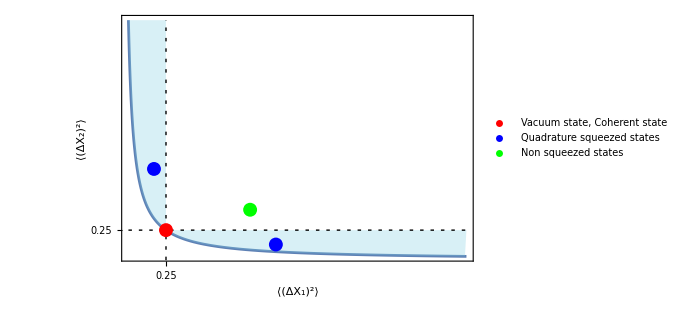

```mathematica
Legended[Show[Plot[1/(16 x),{x,1/32,2},PlotRange->Full,FrameTicks->{{{0.25},None},{{0.25},None}},Epilog->{{Dashing[{0.005,0.01}],Line[{{1/32,0.25},{2,0.25}}]},{Dashing[{0.005,0.01}],Line[{{0.25,0},{0.25,2}}]},{Red,PointSize[0.02],Point[{0.25,0.25}]},{Blue,PointSize[0.02],Point[{0.18,0.76}],Point[{0.89,0.13}]},{Green,PointSize[0.02],Point[{0.74,0.42}]}}],Graphics[{{RGBColor[0.5,0.81,0.89],Opacity[0.3],Polygon[Join[Table[{x,1/(16 x)},{x,1/32,2,0.01}],{{2,0.25},{0.25,0.25},{0.25,2}}  ]]}}],FrameLabel->(Style[#,14]&)/@{"⟨(ΔX_1)^2⟩","⟨(ΔX_2)^2⟩"},Frame->True,ImageSize->500],PointLegend[{Red,Blue,Green},{"Vacuum state, Coherent state","Quadrature squeezed states","Non squeezed states"},LegendFunction->"Panel",LabelStyle->16,LegendMarkerSize->16]]
```

```mathematica
{a,a†} = creationAnnihilation[20];
```

```mathematica
coh = coherentTrunc[a["OutputDimension"]]["Normalize"];
```

```mathematica
αc = RandomComplex[]
```

0.128815+0.65153 ⅈ

Also for a coherent state with a complex α it holds ⟨X_1⟩_α = Re(α)  and ⟨X_2⟩_α = Im(α)

```mathematica
(QuantumMeasurementOperator[N[#]]@ coh[αc])["Mean"]& /@ {X1,X2}
```

{0.128815,0.65153}

Phase space picture its a circle with center (Re(α), Im(α)):

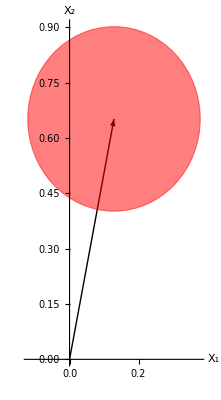

```mathematica
Graphics[
{Arrow[{{0,0},{Re[αc],Im[αc]}}],
EdgeForm[Dashed],Directive[Red],Background->LightBlue,Opacity[0.5],Disk[{Re[αc],Im[αc]},
{Chop[operatorVariance[coh[αc],X1]],Chop[operatorVariance[coh[αc],X2]]}]},
Axes->True,
AxesOrigin->{0,0},
AxesLabel->(Style[#1,14]&)/@{"X_1","X_2"}]
```

Squeezed states are called non-classical because using the Glauber-Sudarshan P function it can be showed if one quadrature variance is < 1/4 implies P(α) is non negative at least in some phase space region. It is also useful to introduce a generic quadrature operator X̂(θ) = 1/2(â  e^(-ⅈ θ)+(â)^† e^(ⅈ θ))

```mathematica
Xθ := QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+a† ⅇ^(ⅈ θ)),"Parameters"->θ];
```

X(0) = X_1 and X(π/2) = X_2

```mathematica
{Xθ[0] == X1, Xθ[Pi/2] == X2}
```

{True,True}

A squeezing  s parameter is defined s(θ) = 4 ⟨(ΔX(θ))^2⟩ - 1, squeezing exists if for some angle -1≤ s(θ) <0

```mathematica
s[ψ_QuantumState,θ_]:= 4 operatorVariance[ψ,Xθ[θ]]-1
```

### Squeezed operator and squeezed vacuum

The unitary squeezed operator is defined as S(ξ) = exp(1/2 ξ^*a^2-1/2 ξ a^(†2)) can be understood as a two photon generalization of displacement operator, where ξ is a complex number ξ = r e^(ⅈ θ), r is called the squeeze parameter 0 ≤ r ≤ ∞

```mathematica
squeeze[ξ_?NumericQ]:= Exp[0.5( Conjugate[ξ](a@a)-ξ (a["Dagger"]@a["Dagger"]))]
```

```mathematica
ξ1 = RandomReal[{0,0.8}]Exp[I RandomReal[{0,2π}]]
```

-0.348041+0.412504 ⅈ

(S(ξ))^† = S(-ξ) = S^-1(ξ)

```mathematica
squeeze[ξ1]["UnitaryQ"]
((squeeze[ξ1]@squeeze[-ξ1])==QuantumOperator["I"[a["OutputDimension"]]])(* Identity operator*)
```

True

True

Using Baker-Hausdorff formula   we get  properties S^†(ξ)a S(ξ)= a cosh r - a^†e^ⅈθ sinh r   and  S^†(ξ)a^† S(ξ)= a^† cosh r - ae^-ⅈθ sinh r
however, in the implementation do not hold exactly because they rely on the commutator [a, a^†] = 1 that is not exact in a truncated Fock space.
Squeezed operator is more numerically sensitive to error because it is a two photon operator ,  the Fock size space have to scale  to larger sizes compared to displacement operator to get accurate numeric results

Squeezed vacuum state  |ξ ⟩ = S(ξ) | 0 ⟩

```mathematica
squeezevacuum = squeeze[ξ1][];
```

The squeeze operator does not change the expectations of X1 and X2

```mathematica
(squeezevacuum["Dagger"]@N[X1]@ squeezevacuum)["Scalar"] //Chop
```

0

```mathematica
(squeezevacuum["Dagger"]@N[X2]@ squeezevacuum)["Scalar"] //Chop
```

0

But the variances we see one got squeezed ( less than 0.25) and the other one increased

```mathematica
operatorVariance[squeezevacuum,X1]//Chop
```

0.620188

```mathematica
operatorVariance[squeezevacuum,X2]//Chop
```

0.20051

It can be derived using the properties of Ŝ on a and a^† that  ⟨Δ X_1⟩^2 = 1/4 [ (cosh(r))^2+(sinh(r))^2-2sinh(r)cosh(r)cos(θ)]
and  ⟨Δ X_2⟩^2 = 1/4 [ (cosh(r))^2+(sinh(r))^2+2sinh(r)cosh(r)cos(θ)]

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.620188,0.20051}

When θ = 0 the expressions reduce to  ⟨Δ X_1⟩^2 = 1/4 e^(-2r)    ⟨Δ X_2⟩^2 = 1/4 e^(2r)
For this case its clearly seen one quadrature gets “squeezed” while the other increases so it maintains the uncertainty principle, also in this case (θ = 0)  the inequality is saturated ( the product of uncertainties equals 1/16 = 0.0625). This is different from a coherent state or Fock state that also saturate the inequality, but they had the same value for the uncertainties in X_1 and X_2.

```mathematica
ξ1 = RandomReal[{0,1.5}]
squeezevacuum = squeeze[ξ1][];
```

0.959288

```mathematica
(operatorVariance[squeezevacuum,#]//Chop)& /@ {X1,X2}
```

{0.036704,1.70281}

```mathematica
1/4{Exp[-2ξ1],Exp[2ξ1]}
```

{0.036704,1.70281}

Phase space representation for the cases with θ = 0 and θ=π (not to scale for visual purposes), in these cases the squeezing is along the axes of X_1 or X_2 describing error ellipses

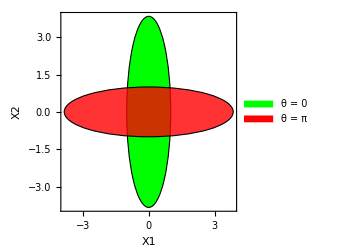

```mathematica
With[{dx =1, dy =operatorVariance[squeezevacuum,X2]/operatorVariance[squeezevacuum,X1]//Log}, 
Legended[
Graphics[{
EdgeForm[Dashed],Green,Disk[{0,0},{dx,dy}],
Opacity[0.8],Red,Disk[{0,0},{dy,dx}]},
Axes->True,
Frame->True,
ImageSize->250,
AxesLabel->{"X1","X2"}],
SwatchLegend[{Green,Red},{"θ = 0", "θ = π"}]]]
```

For a general  ξ = r e^ⅈθ we can defined rotated quadrature operators  Y_1 = cos(θ/2)X_1+ sin(θ/2)X_2  and Y_2= -sin(θ/2)X_1+cos(θ/2)X_2
such that the variances are calculated along the rotated quadrature axes. Because of that reason the value of the variances are  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r)    ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r) .  At  θ = 0   Y_1 and Y_2 reduce to X_1 and X_2

```mathematica
Y1 := QuantumOperator[Cos[θ/2]X1+Sin[θ/2]X2,"Parameters"->θ];
Y2 := QuantumOperator[-Sin[θ/2]X1+Cos[θ/2]X2,"Parameters"->θ];
```

```mathematica
{Y1[0] == X1, Y2[0] == X2}
```

{True,True}

```mathematica
ξ1 = RandomReal[{0,1.}] Exp[I RandomReal[{0,2Pi}]]
```

-0.114113+0.584906 ⅈ

```mathematica
squeezevacuum = squeeze[ξ1][];
```

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, operatorVariance[squeezevacuum,#]& /@ {Y1[θ1],Y2[θ1]}]//Chop
```

{0.0759135,0.823306}

```mathematica
1/4{Exp[-2r],Exp[2r]}/. r->Abs[ξ1]
```

{0.0759135,0.823306}

Phase space picture are rotated ellipses with angle of rotation θ/2  (the dashed lines represent the Y1 and Y2 quadrature axes)

```mathematica
Module[
{θ1=Arg[ξ1],dx =1,dy}, 
dy =operatorVariance[squeezevacuum,Y2[θ1]]/operatorVariance[squeezevacuum,Y1[θ1]] ;
Graphics[{
EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,
Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],
Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
]},
Axes->True,
Frame->True,
ImageSize->Medium,
AxesLabel->{"X1","X2"}]
]
```

-Graphics-

Visualization of the ellipse errors , the product of the variances of X_1 and X_2 only equals the uncertainty limit(1/16)  when the ellipses are alligned with the X_1 and X_2 axes

```mathematica
Manipulate[
Module[
{dx =1/4 Exp[-2r],dy =1/4Exp[2r]}, 
Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,
Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],
Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]],
Text[Framed[(ΔX1)^2 == 1/4(Cosh[r]^2+Sinh[r]^2-2Sinh[r]Cosh[r]Cos[θ1]),
FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.85}],Text[Framed[(ΔX2)^2 == 1/4(Cosh[r]^2+Sinh[r]^2+2Sinh[r]Cosh[r]Cos[θ1]),
FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.55}],Text[Framed[(ΔX1)^2(ΔX2)^2 == 1/16((Cosh[r]^2+Sinh[r]^2)^2-(2Sinh[r]Cosh[r]Cos[θ1])^2),FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.75,-0.75}]
},
Axes->True,
ImageSize->Medium,
AxesLabel->{"X1","X2"},
PlotRange->{{-1,1},{-1,1}},
PlotLabel->"Quadratures of a squeezed vacuum state |ξ⟩"]]
,{{r,0,"Modulus r"},0,1},{{θ1,0,"Argument θ"},0,2π},SaveDefinitions->True]
```

### Squeezed coherent state and displaced squeezed state

A squeezed coherent state is obtained applying the squeeze operator to a coherent state
|ξ, α⟩ = S(ξ)|α⟩ = S(ξ) D(α) |0⟩

```mathematica
squeeze[ξ_?NumericQ]:= Exp[1/2 Conjugate[ξ](a@a)-1/2ξ (a["Dagger"]@a["Dagger"])]
```

```mathematica
{αcoh,ξ1} = RandomReal[{0,2},2]Exp[I RandomReal[{0,2π},2]]
```

{0.888639-0.600672 ⅈ,1.37332-0.262951 ⅈ}

```mathematica
squeezeCoh = squeeze[ξ1]@ disp[αcoh][];
```

⟨ a ⟩ = α cosh(r) - α^* e^ⅈθ sinh(r)

```mathematica
(squeezeCoh["Dagger"]@N[a]@ squeezeCoh)["Scalar"]
```

0.0349671-2.09359 ⅈ

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},αcoh Cosh[r]-Conjugate[αcoh]Exp[I θ] Sinh[r]]
```

0.0349605-2.09365 ⅈ

```mathematica
(*(QuantumMeasurementOperator[N[a]]@ squeezeCoh)["Mean"]  QMO can work with non hermitian operators but only if the mean is real
, for this state is complex so it does not work *)
```

⟨ a^2 ⟩ = α^2 cosh^2(r) + (α^*)^2 e^(2ⅈθ)sinh^2(r)-2|(α|)^2 e^ⅈθ sinh(r)cosh(r)-e^ⅈθ cosh(r)sinh(r)

```mathematica
(squeezeCoh["Dagger"]@N[a@a]@ squeezeCoh)["Scalar"]
```

-8.38976+0.62095 ⅈ

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},αcoh^2 Cosh[r]^2+(αcoh*)^2 Exp[2 ⅈ θ] Sinh[r]^2-2 Abs[αcoh]^2 Exp[ⅈ θ]Sinh[r]Cosh[r]-Exp[I θ]Cosh[r]Sinh[r]]
```

-8.39102+0.621191 ⅈ

⟨ a^† a⟩ = |α|^2(cosh^2(r)+sinh^2(r))-(α*)^2 e^(ⅈ θ)sinh(r)cosh(r)-(α)^2 e^(- ⅈ θ)sinh(r)cosh(r) + sinh^2(r)

```mathematica
(QuantumMeasurementOperator[a†@a]@squeezeCoh)["Mean"]
```

7.99671

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Abs[αcoh]^2(Cosh[r]^2+Sinh[r]^2)+Sinh[r]^2-2Re[(αcoh^2 Exp[-I θ])]Cosh[r]Sinh[r]]//Re
```

7.9968

A more general state called displaced squeezed state is defined as: |α, ξ ⟩ =  D(α) S(ξ)|0⟩, is not the same as a squeezed coherent state because the displacement operator and the squeeze operator do not commute

```mathematica
{a,a†} = creationAnnihilation[120];
```

```mathematica
disp[x_?NumericQ] := Exp[x a["Dagger"]-Conjugate[x] a]
```

```mathematica
αcoh = 2Exp[I RandomReal[{0,2Pi}]]
```

-0.969704-1.74919 ⅈ

Clearly the commutator is not 0

```mathematica
Take[commutator[squeeze[ξ1],disp[αcoh]]["Matrix"]//Diagonal,10]//Normal
```

{0.270544+0.108706 ⅈ,-0.156379+0.140148 ⅈ,-0.521348+0.0690754 ⅈ,0.118651+0.0250509 ⅈ,0.292489-0.0296512 ⅈ,-0.0787196+0.0390296 ⅈ,-0.360586+0.173321 ⅈ,-0.300709+0.217569 ⅈ,-0.124977+0.13135 ⅈ,-0.0850845+0.00266834 ⅈ}

⟨a⟩ = α  	
⟨ a^2⟩ = α^2-e^(ⅈ θ)sinh(r)cosh(r)  	
⟨ a^†a ⟩= |α|^2+(sinh(r))^2
When r → 0, the results for a coherent state are recovered, or when α → 0  the results of squeezed vacuum are recovered

```mathematica
dispSqueezed = disp[αcoh]@ squeeze[ξ1][];
```

```mathematica
{(dispSqueezed["Dagger"]@ a @ dispSqueezed)["Scalar"], αcoh}
```

{-0.969704-1.74919 ⅈ,-0.969704-1.74919 ⅈ}

```mathematica
With[{r = Abs[ξ1],θ1 = Arg[ξ1]},{(dispSqueezed["Dagger"]@ (a@a) @ dispSqueezed)["Scalar"],αcoh^2-ⅇ^(ⅈ θ1)Sinh[r]Cosh[r]}]
```

{-1.97624+2.65883 ⅈ,-1.97624+2.65883 ⅈ}

```mathematica
{(QuantumMeasurementOperator[a†@a]@ dispSqueezed)["Mean"],Abs[αcoh]^2 +Sinh[Abs[ξ1]]^2}
```

{4.39922,4.39922}

For this state it still holds  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r)    ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r)
That can be interpreted that the error ellipses keep their shape for any ξ, the center is displaced by α maintaining the ellipse shape

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, {operatorVariance[dispSqueezed,#]& /@ {Y1[θ1],Y2[θ1]}//Chop,1/4{Exp[-2r],Exp[2r]}}]
```

{{0.0759135,0.823306},{0.0759135,0.823306}}

```mathematica
ξ1 = RandomReal[{0.4,0.7}]Exp[I RandomReal[{0,2Pi}]];αcoh = RandomReal[{1.2,1.5}]Exp[I RandomReal[{0,2Pi}]];
```

```mathematica
Module[{θ1=Arg[ξ1],dx ,dy, h=Re[αcoh], k = Im[αcoh]}, 
dx = operatorVariance[dispSqueezed,Y1[θ1]];dy =operatorVariance[dispSqueezed,Y2[θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{h,k},{dx,dy}],θ1/2],
Black,Dashed,Line[#+{h,k}&/@Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[#+{h,k}& /@ Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
],PointSize[0.022],Point[{h,k}],{Red,Dashing[1,0,0],Arrow[{{0,0},{h,k}}],Text["α",{0.05*h,0}+{h,k}/2]}},
Axes->True,Frame->True,ImageSize->Medium,AxesLabel->{"X1","X2"}]
]
```

-Graphics-

### More properties of squeezed states

For a squeezed vacuum state it can be shown mathematically that  the photon statistics only has non zero values for even number of photons
|ξ ⟩ = 1/(√(cosh(r))) ∑_(m=0)^∞ (-1)^m √((2m)!)/(2^m m!)e^(ⅈ m θ) (tanh(r))^m |2m⟩

```mathematica
ξ2 = RandomReal[{1,2}]Exp[ⅈ RandomReal[{0,2Pi}]];
```

```mathematica
Quiet[(QuantumMeasurementOperator[a†@a]@ squeeze[ξ2][])["Probability"][[1;;10]]];
```

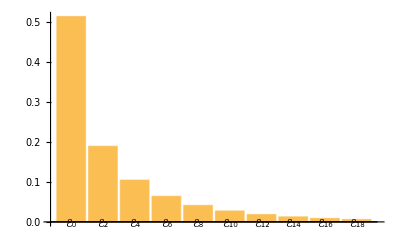

```mathematica
BarChart[%,ChartLabels->Keys[%]]
```

## Generation of squeezed states

A common technique  to generate squeezed light is  to implement parametric processes with the aid of non linear optical devices. A non-linear medium  is pumped by a field of frequency ω_P and photons of the field are converted into pairs of signal photons each of frequency ω = ω_P/2. This is known as degenerate parametric down-conversion

where bis the pump mode, a is the signal mode and χ^(2)is a second order susceptibility

And we can make the approximation that the pump is in a really strong classical field, strong enough to never run out of photons. We can assume the field  is in  a coherent state |β e^(- ι ω_P t)⟩ and operator b and b^† are replaced by  β e^(- ⅈ ω_P t) and β^* e^(ⅈ ω_P t), so the Hamiltonian can be expressed as:

where η = β χ^(2)

Working in the interaction picture:

```mathematica
{a,a†} = creationAnnihilation[20];
```

Time independent term:

```mathematica
H0PA = h ω a†@a;
```

Time dependent term:

```mathematica
HIPA = ⅈ h (η* a@a ⅇ^(ⅈ Subscript[ω, P] t)-η a†@a† ⅇ^(-ⅈ Subscript[ω, P] t));
```

```mathematica
U = QuantumEvolve[H0PA/h,None,t];
```

```mathematica
HI = QuantumOperator[Simplify[U["Dagger"] @ HIPA @ U,Element[{h,Subscript[ω, P],t,ω},Reals]],"Parameters"->{Subscript[ω, P],η}];
```

We get an interaction Hamiltonian , but we consider ω_P = 2 ω that is an energy conserving condition that Hamiltonian becomes time independent

```mathematica
FreeQ[HI[ω,η]["Amplitudes"]//Values,t]
```

False

```mathematica
FreeQ[HI[2ω,η]["Amplitudes"]//Values,t]
```

True

The evolution operator using that interaction Hamiltonian can be shown to take the form of a squeeze operator where ξ = 2 η t
We can check this applying the operators on the vacuum , for the sake of the example we take η = 1

```mathematica
Table[QuantumDistance[Exp[-ⅈ HI[2ω,t]/h][],squeeze[2t][]],{t,0,1.,0.1}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Detection of squeezed state : Homodyne detection

```mathematica
setFockSize[40]
```

```mathematica
a1 = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
a2 = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

```mathematica
st = QuantumState["25",fockBasis];
(st["Dagger"]@ (a1["Dagger"]@a1)@ st)["Scalar"]
(st["Dagger"]@ (a2["Dagger"]@a2)@ st)["Scalar"]
```

2

5

Using a balanced BS it can be proved :   i_34= n_3-n_4=a_3^†a_3-a_4^†a_4=-2[1/(2 ⅈ)(a_2^†a_1-a_1^†a_2)]
n_3-n_4 is related to the photocurrent difference which is an observable with direct experimental interpretation

```mathematica
i34 = -1/ⅈ(a2["Dagger"]@a1-a1["Dagger"]@a2);
```

Given an input state which β being a coherent state and ψ any state : |in⟩ = (|ψ⟩)_1(|β⟩)_2       ⟨n_3-n_4⟩ =  ⟨i_34⟩ = 2 |β | ⟨ X(ϕ+π/2) |ψ⟩
where ϕ is the phase of the complex β. We can define θ = ϕ + π/2 and quadrature at angle θ is defined X(θ) = 1/2(a e^(-ⅈ θ)+ a^†e^(ⅈ θ)), to vary θ we vary ϕ and get different quadrature measurements	. For the variances of the quadratures we get a similar formula
 ⟨(Δ(i_34))^2⟩ = 4 |β |^2 ⟨(Δ( X(θ)))^2⟩

We try also  with a coherent state in the signal port, but has to be weaker than the local oscillator strong coherent field

```mathematica
ψ = coh[0.5+0.72I];
```

```mathematica
osciAmp = 3;
```

```mathematica
cohOsci = QuantumState[coh[osciAmp Exp[I θ]]];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

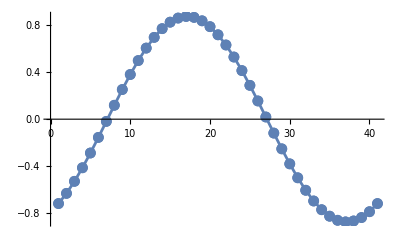

```mathematica
ListLinePlot[{quadratures/6},Mesh->Full]
```

For a coherent state we can extract the parameters easily

```mathematica
{Abs[0.5+0.72I],Max[quadratures]/(2 osciAmp)}
```

{0.876584,0.876385}

```mathematica
quadratures[[{1,1+Quotient[Length@quadratures,4]}]]/(2 osciAmp)
```

{-0.72,0.5}

```mathematica
ξ1 = 0.15 Exp[ⅈ RandomReal[{0,2π}]]
```

-0.0769251-0.128773 ⅈ

```mathematica
Xtheta[θ_?NumericQ]:= 1/2(a Exp[-ⅈ θ]+a["Dagger"]Exp[ⅈ θ])
```

For a squeezed vacuum the expectation of the quadratures is zero

```mathematica
ψ = squeeze[ξ1][];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

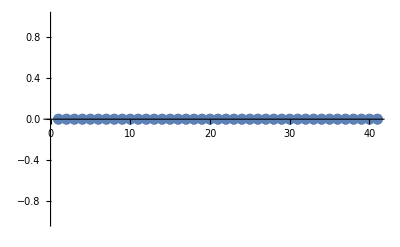

```mathematica
ListLinePlot[{quadratures/6},Mesh->Full]
```

But not the variances

```mathematica
ψ = squeeze[ξ1] @coh[0.5+0.72I];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

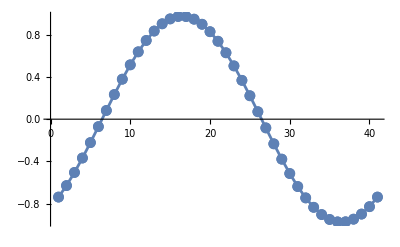

```mathematica
ListLinePlot[{quadratures/(2 osciAmp)},Mesh->Full]
```

```mathematica
quadratures2 = Table[(ψ["Dagger"]@Xtheta[x-Pi/2] @ ψ)["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

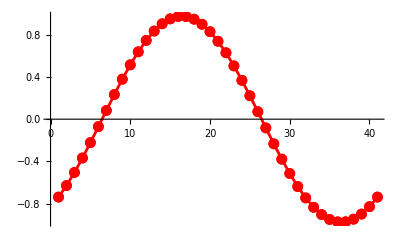

```mathematica
ListLinePlot[quadratures2,Mesh->Full,PlotStyle->Red]
```

```mathematica
variances = Table[operatorVariance[in[x],N[i34]]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

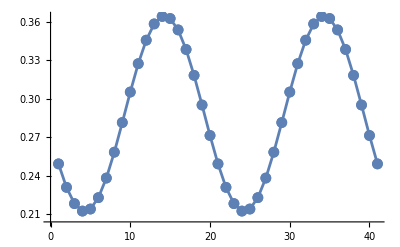

```mathematica
ListLinePlot[variances / (4 osciAmp^2),Mesh->Full]
```

```mathematica
variances2 = Table[operatorVariance[ψ,Xtheta[x-Pi/2]]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

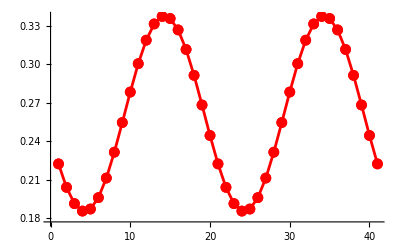

```mathematica
ListLinePlot[variances2,Mesh->Full,PlotStyle->Red]
```

## Number squeezed states

## Schrodinger cat states

## Two-mode squeezed vacuum states